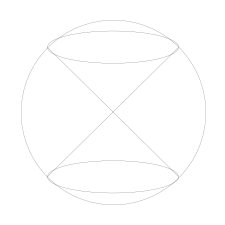

```mathematica
r = 10;

g1 = Graphics[{Thickness[0.0001],Circle[{0,0},r]}];

g2 = Graphics[{Thickness[0.0001],Line[
						{{r(√2)/2,r(√2)/2-0.09},{r(-√2)/2,r(-√2)/2+0.09}}
						]}];
g3 = Graphics[{Thickness[0.0001],Line[
						{{r(-√2)/2,r(√2)/2-0.09},{r(√2)/2,r(-√2)/2+0.09}}
						]}];

												
g4 = Graphics[{Thickness[0.0001],Circle[{0,r(√2)/2-0.05},{r(√2)/2+0.025,1.75}]}];
g5 = Graphics[{Thickness[0.0001],Circle[{0,-r(√2)/2+0.05},{r(√2)/2+0.025,1.75}]}];
Show[g1,g2,g3,g4,g5]
```

```mathematica
Clear[r,r1,h,x,y,z,t]


r=10;
h = 0.75r;
r1 =√(r^2-h^2);

cocolor=RGBColor[0.65,0.15,0.08];
spcolor=RGBColor[0.21,0.27,0.86];

cocolor2=RGBColor[0.17,0.,0.43]
(*
RGBColor[0.25,0.17,0.57];
*)

p1 = ParametricPlot3D[{r1 Cos[t],r1 Sin[t],h},{t,0,2π},PlotStyle->Red,PlotRange->{{-10,10},{-10,10},{-10,10}},Boxed->False,Axes->False];
p2 = ParametricPlot3D[{r1 Cos[t],r1 Sin[t],-h},{t,0,2π},PlotStyle->Red,PlotRange->{{-10,10},{-10,10},{-10,10}},Boxed->False,Axes->False];

p3 = ContourPlot3D[x^2+y^2+z^2==r^2,{x,-r,r},{y,-r,r},{z,-r,r},
	Mesh->None,ContourStyle->Directive[Blue,Opacity[0.2],Specularity[White,30]],Boxed->False,Axes->False,
	ViewPoint->{2.742678460259541,-1.4860972690029237,1.3111940248073273},
	ViewVertical->{-0.37719632682989207,-0.30465151529137136,0.8745915533874706}];

p4 = Graphics3D[{EdgeForm[{Thick,cocolor}],cocolor2,Opacity[0.3],Cone[{{0,0,-h},{0,0,0}},r1]},Boxed->False,Axes->False];
p5 = Graphics3D[{EdgeForm[{Thick,cocolor}],cocolor2,Opacity[0.3],Cone[{{0,0,h},{0,0,0}},r1]},Boxed->False,Axes->False];

p6 = Graphics3D[{Thick,cocolor,Line[{{r1,0,h},{-r1,0,-h}}]}];
p7 = Graphics3D[{Thick,cocolor,Line[{{-r1,0,h},{r1,0,-h}}]}];

p8 = ParametricPlot3D[{r Cos[t],0,r Sin[t]},{t,0,2π},PlotStyle->spcolor,PlotRange->{{-10,10},{-10,10},{-10,10}},Boxed->False,Axes->False,
	ViewPoint->{2.742678460259541,-1.4860972690029237,1.3111940248073273},
	ViewVertical->{-0.37719632682989207,-0.30465151529137136,0.8745915533874706}];

img = Show[p3,p4,p5,p6,p7,p8]
```

RGBColor[0.17, 0., 0.43]

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]]
Export["favicon2.png",img,Background -> None, ImageSize->{1000,1000},ImageResolution->100]
img=Import["favicon2.png"];
img=ImageCrop[img];
Export["favicon2.png",img,Background -> None, ImageSize->{1000,1000},ImageResolution->100]
```

C:\Users\fuserofworlds\Google Drive\root

favicon2.png

favicon2.png

```mathematica
(*Original coloring*)

Clear[r,r1,h,x,y,z,t]


r=10;
h = 0.75r;
r1 =√(r^2-h^2);

cocolor=RGBColor[0.65,0.15,0.08];
spcolor=RGBColor[0.21,0.27,0.86]
cocolor2=Red;
(*

*)

p1 = ParametricPlot3D[{r1 Cos[t],r1 Sin[t],h},{t,0,2π},PlotStyle->Red,PlotRange->{{-10,10},{-10,10},{-10,10}},Boxed->False,Axes->False];
p2 = ParametricPlot3D[{r1 Cos[t],r1 Sin[t],-h},{t,0,2π},PlotStyle->Red,PlotRange->{{-10,10},{-10,10},{-10,10}},Boxed->False,Axes->False];

p3 = ContourPlot3D[x^2+y^2+z^2==r^2,{x,-r,r},{y,-r,r},{z,-r,r},
	Mesh->None,ContourStyle->Directive[Blue,Opacity[0.2],Specularity[White,30]],Boxed->False,Axes->False,
	ViewPoint->{2.742678460259541,-1.4860972690029237,1.3111940248073273},
	ViewVertical->{-0.37719632682989207,-0.30465151529137136,0.8745915533874706}];

p4 = Graphics3D[{EdgeForm[{Thick,cocolor}],cocolor2,Opacity[0.3],Cone[{{0,0,-h},{0,0,0}},r1]},Boxed->False,Axes->False];
p5 = Graphics3D[{EdgeForm[{Thick,cocolor}],cocolor2,Opacity[0.3],Cone[{{0,0,h},{0,0,0}},r1]},Boxed->False,Axes->False];

p6 = Graphics3D[{Thick,cocolor,Line[{{r1,0,h},{-r1,0,-h}}]}];
p7 = Graphics3D[{Thick,cocolor,Line[{{-r1,0,h},{r1,0,-h}}]}];

p8 = ParametricPlot3D[{r Cos[t],0,r Sin[t]},{t,0,2π},PlotStyle->spcolor,PlotRange->{{-10,10},{-10,10},{-10,10}},Boxed->False,Axes->False,
	ViewPoint->{2.742678460259541,-1.4860972690029237,1.3111940248073273},
	ViewVertical->{-0.37719632682989207,-0.30465151529137136,0.8745915533874706}];

img = Show[p3,p4,p5,p6,p7,p8]
```

RGBColor[0.21, 0.27, 0.86]

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]]
Export["favicon.png",img,Background -> None, ImageSize->{1000,1000},ImageResolution->100]
img=Import["favicon.png"];
img=ImageCrop[img];
Export["favicon.png",img,Background -> None, ImageSize->{1000,1000},ImageResolution->100]
```

C:\Users\fuserofworlds\Google Drive\root

favicon.png

favicon.png